```mathematica
SetDirectory[NotebookDirectory[]];
countryWideConfirmed=Import["./COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv","CSV"];
```

```mathematica
countryWideConfirmedExChina = DeleteCases[countryWideConfirmed,{_,"China",__}];
countryWideConfirmedExChina=Drop[countryWideConfirmedExChina,1,{1,4}];
globalConfirmedExChina = Transpose[{Total[countryWideConfirmedExChina,{1}]}];
dataGlobal=MapThread[Prepend,{globalConfirmedExChina,Table[a,{a,0,Length[globalConfirmedExChina]-1,1}]}]

confirmedUS = Cases[countryWideConfirmed,{_,"US",__}];
confirmedUS=Transpose[Drop[confirmedUS,0,{1,4}]];
dataUS=MapThread[Prepend,{confirmedUS,Table[a,{a,0,Length[confirmedUS]-1,1}]}]
```

{{0,7},{1,11},{2,21},{3,28},{4,43},{5,50},{6,69},{7,79},{8,93},{9,125},{10,147},{11,157},{12,165},{13,185},{14,195},{15,207},{16,281},{17,306},{18,321},{19,408},{20,416},{21,462},{22,473},{23,527},{24,617},{25,711},{26,824},{27,925},{28,1020},{29,1120},{30,1269},{31,1571},{32,1936},{33,2320},{34,2652},{35,3222},{36,4146},{37,5184},{38,6655},{39,8437},{40,10170},{41,12579},{42,14734},{43,17349},{44,21111},{45,25077},{46,28998},{47,32730},{48,37733},{49,44954},{50,47420},{51,64260},{52,75124},{53,86451},{54,100541},{55,116044},{56,133719},{57,161344},{58,190785},{59,223091},{60,255518},{61,296737},{62,336454},{63,385992},{64,447809}}

{{0,1},{1,1},{2,2},{3,2},{4,5},{5,5},{6,5},{7,5},{8,5},{9,7},{10,8},{11,8},{12,11},{13,11},{14,11},{15,11},{16,11},{17,11},{18,11},{19,11},{20,12},{21,12},{22,13},{23,13},{24,13},{25,13},{26,13},{27,13},{28,13},{29,13},{30,15},{31,15},{32,15},{33,51},{34,51},{35,57},{36,58},{37,60},{38,68},{39,74},{40,98},{41,118},{42,149},{43,217},{44,262},{45,402},{46,518},{47,583},{48,959},{49,1281},{50,1663},{51,2179},{52,2727},{53,3499},{54,4632},{55,6421},{56,7783},{57,13677},{58,19100},{59,25489},{60,33276},{61,43847},{62,53740},{63,65778},{64,83836}}

```mathematica
lessFancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)),c[0]==c0},c,{t,0,110}]]]
fancyFitUS=NonlinearModelFit[dataUS,{lessFancyModel[rr,kk,pp,c00][t]},{{rr,.1},kk,pp,c00},t]
fancyFitUS["ParameterConfidenceIntervalTable"]
fancyFitUS["RSquared"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
rr | 0.188901 | 0.0740859 | {0.040757,0.337045}
kk | 154962. | 17141.3 | {120686.,189238.}
pp | 1.05996 | 0.0413813 | {0.977212,1.14271}
c00 | 0.0428197 | 0.111702 | {-0.180543,0.266182}

0.999022

179434./(1+350.255 ⅇ^(15.7722-0.335484 t))

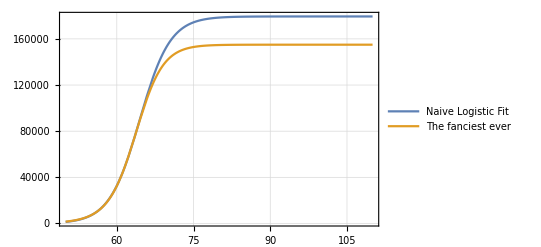

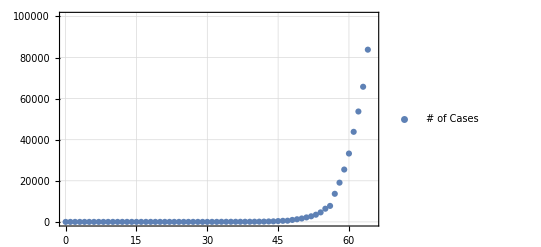

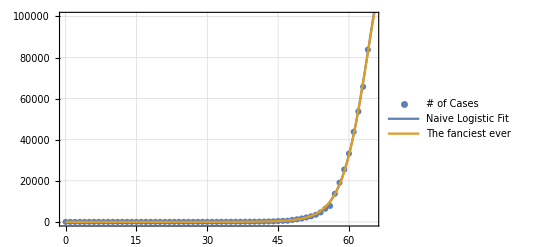

```mathematica
fitLogUS=NonlinearModelFit[dataUS,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fitLogUS]
Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,50,110},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotUS=ListPlot[dataUS,PlotRange->{{0,65},{0,100000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsUS=Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotUS,fitPlotsUS]
```

```mathematica
fancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ,a_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)^a),c[0]==c0},c,{t,0,110}]]]
fancyFitGlobal=NonlinearModelFit[dataGlobal,{fancyModel[r,k,p,c0,a][t]},{{r,.2},k,p,c0,{a,1}},t]
fancyFitGlobal["ParameterConfidenceIntervalTable"]
fancyFitGlobal["RSquared"]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
r | 0.262748 | 0.0800139 | {0.102696,0.422799}
k | 1.16352×10^6 | 1.32988×10^6 | {-1.49664×10^6,3.82369×10^6}
p | 0.956781 | 0.028911 | {0.89895,1.01461}
c0 | 2.0957 | 3.36658 | {-4.63846,8.82986}
a | 2.12596 | 2.64347 | {-3.16178,7.41369}

0.999825

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(2.03576×10^6)/(1+96.8776 ⅇ^(7.45765-0.168095 t))

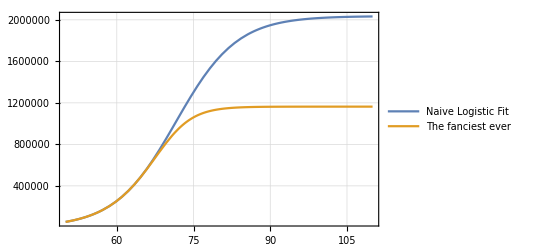

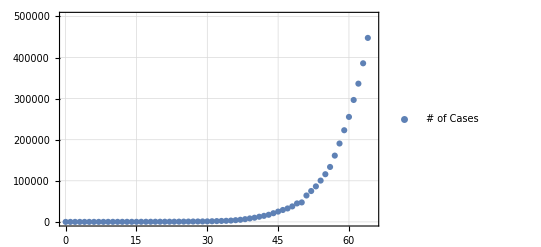

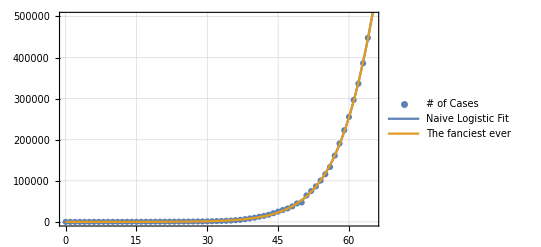

```mathematica
fitLogGlobal=NonlinearModelFit[dataGlobal,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fitLogGlobal]
Plot[{Normal[fitLogGlobal],Normal[fancyFit]},{t,50,110},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotGlobal=ListPlot[dataGlobal,PlotRange->{{0,65},{0,500000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsGlobal=Plot[{Normal[fitLogGlobal],Normal[fancyFitGlobal]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotGlobal,fitPlotsGlobal]
```